# Information FFL C2

```mathematica
Subscript[K, px]=200 ; (*Tasa de sintesis de proteina X*)
Subscript[K, py]=300;  (*Tasa de sintesis de proteina Y*)
Subscript[K, pz]=100 ; (*Tasa de sintesis de proteina Z*)

Hill=2 ;

Subscript[γ, x]=1/5;      (*Tasa de degradación de ARNmX*)
Subscript[γ, y]=1/7 ;      (*Tasa de degradación de ARNmY*)
Subscript[γ, z]=1/10 ;     (*Tasa de degradación de ARNmZ*)

Subscript[μ, x]=1/20 ;   (*Tasa de degradación de proteina X*)
Subscript[μ, y]=1/40;    (*Tasa de degradación de proteina Y*)
Subscript[μ, z]=1/30 ;   (*Tasa de degradación de proteina Z*)

Subscript[M, x] = Subscript[K, x]/Subscript[γ, x];     (*Valor estado estacionario de ARNm X*)
X=Subscript[K, px]/Subscript[μ, x] Subscript[M, x];  (*Valor estado estacionario de proteina X*)

Subscript[M, y] = 10;
Subscript[M, z] = 25;

Y = Subscript[K, py]/Subscript[μ, y] Subscript[M, y];

Z = N[Subscript[K, pz]/Subscript[μ, z] Subscript[M, z]];

Subscript[K, xy]=X;
Subscript[K, xz]=X;
Subscript[K, yz]=2Y;

Subscript[K, y]=N[Subscript[M, y] Subscript[γ, y]((X^Hill+Subscript[K, xy]^Hill)/Subscript[K, xy]^Hill)]; (*YA*)

Subscript[K, z]=Subscript[M, z] Subscript[γ, z](((Y^Hill+Subscript[K, yz]^Hill)(X^Hill+Subscript[K, xz]^Hill))/(X^Hill Subscript[K, yz]^Hill));(*YA*)

FuncionHillY[X_]:=Subscript[K, y] Subscript[K, xy]^Hill/(X^Hill+Subscript[K, xy]^Hill);(*YA*)

FuncionHillZ[Y_, X_]:=Subscript[K, z](Subscript[K, yz]^Hill     X^Hill)/((Y^Hill+Subscript[K, yz]^Hill)(X^Hill+Subscript[K, xz]^Hill)); (*YA*)

DerivadaFuncionHillYX[X_]:=-Subscript[K, y](Hill Subscript[K, xy]^Hill X^(Hill-1))/((X^Hill + Subscript[K, xy]^Hill)^2);

DerivadaFuncionHillZX[X_,Y_]:=Subscript[K, z](Subscript[K, yz]^Hill Hill  Subscript[K, xz]^Hill  X^(Hill-1))/((Y^Hill+Subscript[K, yz]^Hill)(X^Hill+Subscript[K, xz]^Hill)^2);

DerivadaFuncionHillZY[X_,Y_]:=-Subscript[K, z](Subscript[K, xz]^Hill Hill Subscript[K, yz]^Hill Y^(Hill-1))/((X^Hill+Subscript[K, xz]^Hill)(Y^Hill+Subscript[K, yz]^Hill)^2);


Jaccobiano2 = Refine[{{-Subscript[γ, x],0,0,0,0,0}, {0,-Subscript[γ, y],0,DerivadaFuncionHillYX[X],0,0}, {0,0,-Subscript[γ, z],DerivadaFuncionHillZX[X,Y],DerivadaFuncionHillZY[X,Y],0}, {Subscript[K, px],0,0,-Subscript[μ, x],0,0}, {0,Subscript[K, py],0,0,-Subscript[μ, y],0}, {0,0,Subscript[K, pz],0,0,-Subscript[μ, z]}}, Assumptions ->{ Subscript[γ, x]>0,Subscript[γ, y]>0,Subscript[γ, z]>0, Subscript[μ, x]>0, Subscript[μ, y]>0 , Subscript[μ, z]>0, Subscript[K, px] >0, Subscript[K, py]>0, Subscript[K, pz]>0,Element[Subscript[γ, x],Reals], Element[Subscript[γ, y],Reals], Element[Subscript[γ, z],Reals], Element[Subscript[μ, x],Reals], Element[Subscript[μ, y],Reals], Element[Subscript[μ, z],Reals],Element[Subscript[K, px],Reals],Element[Subscript[K, py],Reals],Element[Subscript[K, pz],Reals]}];

Difusion2 =- {{Subscript[δ, mx]}, {Subscript[δ, my]}, {Subscript[δ, mz]}, {Subscript[δ, x]}, {Subscript[δ, y]}, {Subscript[δ, z]}}. {{Subscript[δ, mx]}, {Subscript[δ, my]}, {Subscript[δ, mz]}, {Subscript[δ, x]}, {Subscript[δ, y]}, {Subscript[δ, z]}}ᵀ /.{ Subscript[δ, mx] Subscript[δ, my]-> 0,Subscript[δ, mx] Subscript[δ, mz]-> 0,Subscript[δ, mx] Subscript[δ, x]-> 0,Subscript[δ, mx] Subscript[δ, y]-> 0,Subscript[δ, mx] Subscript[δ, z]-> 0, Subscript[δ, my] Subscript[δ, mz]-> 0,Subscript[δ, my] Subscript[δ, x]-> 0,Subscript[δ, my] Subscript[δ, y]-> 0,Subscript[δ, my] Subscript[δ, z]-> 0, Subscript[δ, mz] Subscript[δ, x]-> 0,Subscript[δ, mz] Subscript[δ, y]-> 0,Subscript[δ, mz] Subscript[δ, z]-> 0, Subscript[δ, x] Subscript[δ, y]-> 0,Subscript[δ, x] Subscript[δ, z]-> 0, Subscript[δ, y] Subscript[δ, z]-> 0, Subscript[δ, mx] Subscript[δ, mx]-> 2 Subscript[γ, x] Subscript[M, x], Subscript[δ, my] Subscript[δ, my]-> 2 Subscript[γ, y] Subscript[M, y], Subscript[δ, mz] Subscript[δ, mz]-> 2 Subscript[γ, z] Subscript[M, z], Subscript[δ, x] Subscript[δ, x]-> 2 Subscript[μ, x] X, Subscript[δ, y] Subscript[δ, y]-> 2 Subscript[μ, y] Y, Subscript[δ, z] Subscript[δ, z]-> 2 Subscript[μ, z] Z };
```

```mathematica
MatricesCovarianzas = Table[LyapunovSolve[Jaccobiano2, Difusion2],{Subscript[K, x],50}];
```

```mathematica
valorEsperadoX = Table[Subscript[K, px]/Subscript[μ, x] Subscript[K, x]/Subscript[γ, x] , {Subscript[K, x],50}];

valorEsperadoY = Table[Subscript[K, py]/Subscript[μ, y] Subscript[M, y], {Subscript[K, x],50}];

valorEsperadoZZ = Table[Subscript[K, pz]/Subscript[μ, z] Subscript[M, z], {Subscript[K, x],50}];

RuidoYX = Table[(MatricesCovarianzas[[indice]][[4,5]])/(valorEsperadoX[[indice]]valorEsperadoY[[indice]]),{indice,50}];

RuidoZX = Table[(MatricesCovarianzas[[indice]][[4,6]])/(valorEsperadoX[[indice]]*valorEsperadoZZ[[indice]]),{indice,50}];

RuidoZY =  Table[(MatricesCovarianzas[[indice]][[5,6]])/(valorEsperadoY[[indice]]*valorEsperadoZZ[[indice]]),{indice,50}];
```

```mathematica
RuidoFFLC2 = {RuidoYX,RuidoZX, RuidoZY };

Export["Ruido_FFL_C2_Hill2.csv",RuidoFFLC2,"CSV"]
```

Ruido_FFL_C2_Hill2.csv

```mathematica
InformacionYXvariante = Table[1/2 Log[2,(MatricesCovarianzas[[indice]][[5,5]]*MatricesCovarianzas[[indice]][[4,4]])/(MatricesCovarianzas[[indice]][[5,5]]*MatricesCovarianzas[[indice]][[4,4]] -(MatricesCovarianzas[[indice]][[5,4]])^2 )], {indice,50}];

InformacionZXvariante = Table[1/2 Log[2,(MatricesCovarianzas[[indice]][[6,6]]*MatricesCovarianzas[[indice]][[4,4]])/(MatricesCovarianzas[[indice]][[6,6]]*MatricesCovarianzas[[indice]][[4,4]] -(MatricesCovarianzas[[indice]][[6,4]])^2 )], {indice,50}];

InformacionZYvariante = Table[1/2 Log[2,(MatricesCovarianzas[[indice]][[6,6]]*MatricesCovarianzas[[indice]][[5,5]])/(MatricesCovarianzas[[indice]][[6,6]]*MatricesCovarianzas[[indice]][[5,5]] -(MatricesCovarianzas[[indice]][[6,5]])^2 )], {indice,50}];

InformacionZXYvariante = Table[1/2 Log[2,(MatricesCovarianzas[[indice]][[6,6]]*MatricesCovarianzas[[indice]][[5,5]]*MatricesCovarianzas[[indice]][[4,4]]-(MatricesCovarianzas[[indice]][[5,4]])^2)/Det[MatricesCovarianzas[[indice]][[4;;6,4;;6]]]], {indice,50}]
```

{0.213431,0.129108,0.0983701,0.0824217,0.072653,0.0660537,0.0612961,0.0577035,0.0548946,0.0526381,0.0507856,0.0492375,0.0479245,0.0467967,0.0458177,0.0449597,0.0442016,0.043527,0.0429227,0.0423784,0.0418854,0.041437,0.0410272,0.0406513,0.0403053,0.0399857,0.0396897,0.0394147,0.0391585,0.0389193,0.0386954,0.0384855,0.0382882,0.0381025,0.0379273,0.0377618,0.0376052,0.0374568,0.037316,0.0371822,0.0370549,0.0369337,0.036818,0.0367076,0.0366021,0.0365011,0.0364045,0.0363118,0.0362229,0.0361376}

```mathematica
informacionFFLC2 = {InformacionYXvariante,InformacionZXvariante, InformacionZYvariante, InformacionZXYvariante }

Export["datos_FFL_C2_Hill1.csv",informacionFFLC2,"CSV"];
```

{{0.0387472,0.0213779,0.0147613,0.0112725,0.00911761,0.00765437,0.00659584,0.00579451,0.0051668,0.00466179,0.00424672,0.00389951,0.00360479,0.00335149,0.00313145,0.00293852,0.00276799,0.00261616,0.00248012,0.00235753,0.00224649,0.00214544,0.00205309,0.00196836,0.00189035,0.00181828,0.00175151,0.00168947,0.00163167,0.0015777,0.00152718,0.0014798,0.00143527,0.00139334,0.00135379,0.00131643,0.00128107,0.00124756,0.00121576,0.00118554,0.00115679,0.0011294,0.00110327,0.00107833,0.00105449,0.00103168,0.00100984,0.000988898,0.000968811,0.000949524},{0.0578294,0.0350232,0.0251189,0.0195817,0.0160448,0.0135902,0.011787,0.0104062,0.00931507,0.00843102,0.00770022,0.00708601,0.00656255,0.00611111,0.00571778,0.00537202,0.00506569,0.00479241,0.00454711,0.0043257,0.00412485,0.00394182,0.00377435,0.00362053,0.00347875,0.00334766,0.00322609,0.00311304,0.00300764,0.00290915,0.00281691,0.00273033,0.00264892,0.00257222,0.00249984,0.00243142,0.00236664,0.00230523,0.00224693,0.0021915,0.00213874,0.00208846,0.00204049,0.00199467,0.00195087,0.00190895,0.00186879,0.00183029,0.00179334,0.00175785},{0.143819,0.0858527,0.0669876,0.0577965,0.0523904,0.0488405,0.0463344,0.0444725,0.0430353,0.0418928,0.040963,0.0401917,0.0395415,0.0389862,0.0385063,0.0380876,0.037719,0.037392,0.0371,0.0368377,0.0366007,0.0363856,0.0361895,0.0360099,0.0358449,0.0356927,0.0355519,0.0354213,0.0352999,0.0351866,0.0350807,0.0349815,0.0348883,0.0348007,0.0347182,0.0346402,0.0345666,0.0344968,0.0344307,0.0343679,0.0343081,0.0342513,0.0341971,0.0341454,0.034096,0.0340488,0.0340036,0.0339603,0.0339187,0.0338789},{0.213431,0.129108,0.0983701,0.0824217,0.072653,0.0660537,0.0612961,0.0577035,0.0548946,0.0526381,0.0507856,0.0492375,0.0479245,0.0467967,0.0458177,0.0449597,0.0442016,0.043527,0.0429227,0.0423784,0.0418854,0.041437,0.0410272,0.0406513,0.0403053,0.0399857,0.0396897,0.0394147,0.0391585,0.0389193,0.0386954,0.0384855,0.0382882,0.0381025,0.0379273,0.0377618,0.0376052,0.0374568,0.037316,0.0371822,0.0370549,0.0369337,0.036818,0.0367076,0.0366021,0.0365011,0.0364045,0.0363118,0.0362229,0.0361376}}

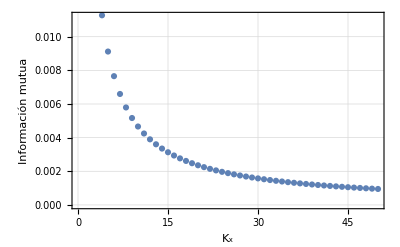

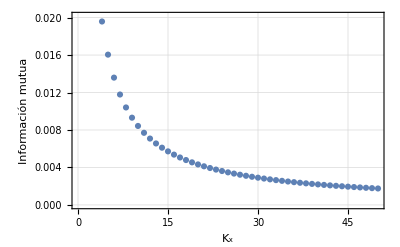

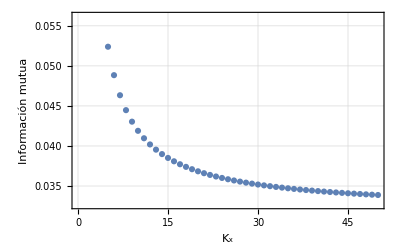

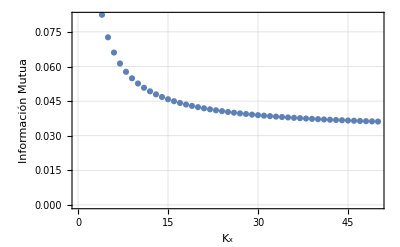

```mathematica
ListPlot[{Range[1,50],InformacionYXvariante }ᵀ, Frame->True, FrameStyle->Black, FrameLabel->{{"Información mutua",None}, {"K_x","Información mutua I(Y;X)"}}, GridLines->Automatic]

ListPlot[{Range[1,50],InformacionZXvariante }ᵀ, Frame->True, FrameStyle->Black, FrameLabel->{{"Información mutua",None}, {"K_x","Información mutua I(Z;X)"}}, GridLines->Automatic]

ListPlot[{Range[1,50],InformacionZYvariante }ᵀ, Frame->True, FrameStyle->Black, FrameLabel->{{"Información mutua",None}, {"K_x","Información Mutua I(Z;Y)"}}, GridLines->Automatic]

ListPlot[{Range[1,50],InformacionZXYvariante }ᵀ, Frame->True, FrameStyle->Black, FrameLabel->{{"Información Mutua",None}, {"K_x","Información Mutua I(Z;X,Y)"}}, GridLines->Automatic]
```

```mathematica
Table[a,{a,50}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}